## Phase Velocity v. Depth

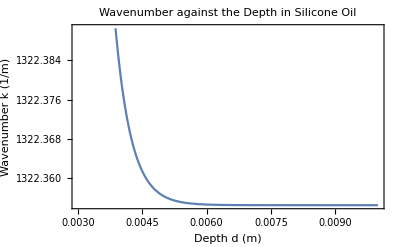

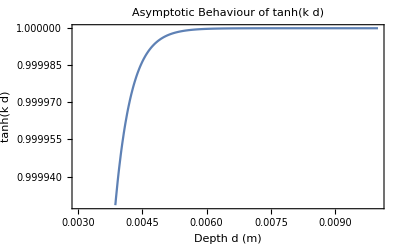

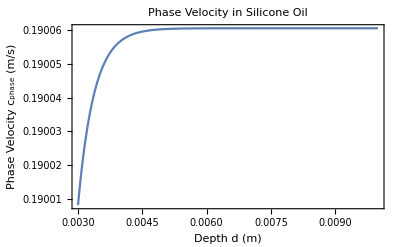

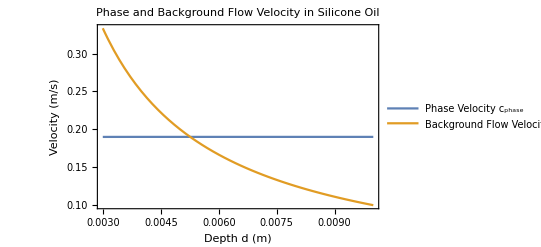

0.00526148479470950678382196608387

```mathematica
(* ----------------- Dispersion Relation ---------------- *)
dispersion[k_,d_]:=g k(1 +  k^2 l^2)Tanh[k d];

(* --------------- System Parameters ------------------ *)
σ=20.6*10^-3 ;                (* Surface tension of Silicone oil (kg/s^2) *)
ρ=949 ;                              (* Density of Silicone oil (kg/m^3) *)
g=9.81;                             (* Gravitational acceleration (m/s^2) *)
l=Sqrt[σ/(ρ g)];    (* Capillary Length (m)*)
ω = 80π;                            (* Resonent Frequency of Waves *)

(* --------------- k Solver ------------- *)
kSol[d_?NumericQ] :=Module[{kinit},
	kinit=ω^2/g; (* initial k *)
	k/.Quiet[
		FindRoot[dispersion[k,d]==ω^2,{k,kinit},
		WorkingPrecision->20,(*plenty of digits*)
		AccuracyGoal->12,
		PrecisionGoal->12]
		]
]

(* ----------- Phase Speed Solver ---------- *)
PhaseVel[d_?NumericQ]:=ω/kSol[d];

(* ---------- Background Flow Solver -------- *)
Flux = 0.001;
vB[d_?NumericQ]:=Flux/d;

(* ----------- Phase Speed & k Plot ------------ *)
dMin = 3*10^-3; (* m *)
dMax = 10*10^-3; (* m *)
Plot[{kSol[d]},{d,dMin,dMax},
			Frame->True,
			FrameLabel->{"Depth  d  (m)","Wavenumber  k  (1/m)"},
			PlotLabel->"Wavenumber against the Depth in Silicone Oil"]
Plot[{Tanh[kSol[d]d]},{d,dMin,dMax},
			Frame->True,
			FrameLabel->{"Depth  d  (m)","tanh(k d)"},
			PlotLabel->"Asymptotic Behaviour of tanh(k d)"]
Plot[{PhaseVel[d]},{d,dMin,dMax},
			Frame->True,
			FrameLabel->{"Depth  d  (m)","Phase Velocity c_phase (m/s)"},
			PlotLabel->"Phase Velocity in Silicone Oil",
			PlotRange->Full]
Plot[{PhaseVel[d],vB[d]},{d,dMin,dMax},
			Frame->True,
			PlotLegends->{"Phase Velocity c_phase","Background Flow Velocity v_B"} ,
			FrameLabel->{"Depth  d  (m)","Velocity  (m/s)"},
			PlotLabel->"Phase and Background Flow Velocity in Silicone Oil",
			PlotRange->Full]

(* ---------- Event Horizon Depth ------------ *)
dEH=d/.FindRoot[PhaseVel[d]==vB[d],{d,Mean[{dMin,dMax}]},WorkingPrecision->30]
```